```mathematica
t4cplusplus =Import["/Users/lucamarsili/Documents/IFIC/GUT/DW/A4_DW/build1/bin/A4Z2_DW_t4_beta2.dat"]
```

8.16667×10^-7[{{z,phi0,phi1,phi2,density}}]

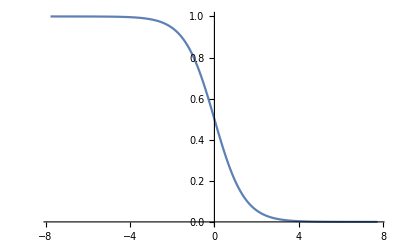

```mathematica
Listc=Table[{t4cplusplus[[i,1]],t4cplusplus[[i,2]]},{i,2,400}];
ListLinePlot[Listc]
```

```mathematica
zt4python = Import["/Users/lucamarsili/Documents/IFIC/GUT/DW/CosmoTransitions/profile1Dzeta_Z2.dat"];
```

```mathematica
(* phi0 c++ is phi2 python, phi2 c++ is phi0 python*)
```

```mathematica
Listp=Table[{zt4python[[i,1]], Phit4python[[i,1]]},{i,1,399}];
```

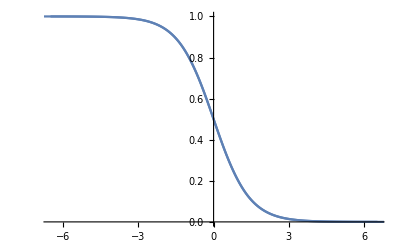

```mathematica
Show[ListLinePlot[Listp,PlotRange->Full],ListLinePlot[Listc]]
```